Correlação entre a probabilidade da regra e a proporção de ss na trinca. E correlação da probabilidade da regra e proporção de acertos na predição.

```mathematica
dataPFC = Import["~/Documents/PhD-quali/zeca-analise/prob_freq_c.csv"]
```

{{AAA,0,181,0.,1.,0.131445,181.,0.},{AAC,0,22,0.,1.,0.146667,22.,0.102},{AAD,2,193,0.0102564,0.989744,0.358456,195.,0.3036},{AAE,2,108,0.0181818,0.981818,0.138539,110.,0.1256},7950,{YYV,3,8,0.272727,0.727273,0.0964912,11.,0.3394},{YYW,4,3,0.571429,0.428571,0.304348,7.,0.1816},{YYY,11,3,0.785714,0.214286,0.164706,14.,0.2276}}
 |  |  |  |

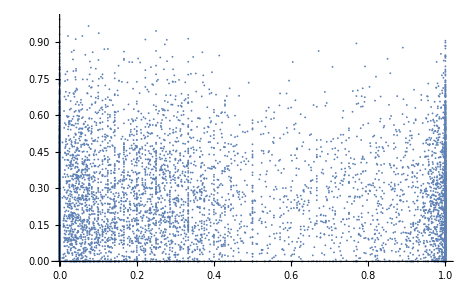

```mathematica
ListPlot[dataPFC[[All,{4,8}]]]
```

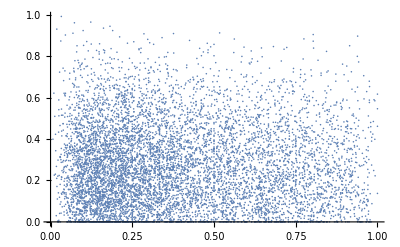

```mathematica
ListPlot[dataPFC[[All,{6,8}]]]
```

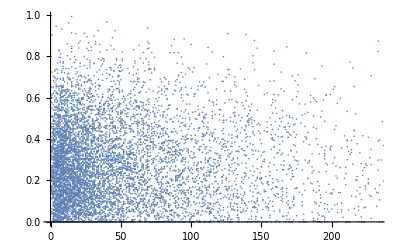

```mathematica
ListPlot[dataPFC[[All,{7,8}]]]
```

```mathematica
IndependenceTest[dataPFC[[All,6]], dataPFC[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is not rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | -0.00442008 | 0.432582
Goodman-Kruskal γ | -0.00848904 | 0.258099
Hoeffding 𝒟 | 0.000032892 | 0.197645
Kendall τ | -0.00847142 | 0.258053
Spearman Rank | -0.0127336 | 0.25607, | Statistic
Spearman Rank | -0.0127336}

```mathematica
IndependenceTest[dataPFC[[All,4]], dataPFC[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | -0.0179828 | 0.111381
Goodman-Kruskal γ | -0.0176602 | 0.0320994
Hoeffding 𝒟 | 0.000129481 | 0.0407782
Kendall τ | -0.0168206 | 0.030444
Spearman Rank | -0.0242654 | 0.0304256, | Statistic
Spearman Rank | -0.0242654}

```mathematica
IndependenceTest[dataPFC[[All,7]], dataPFC[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is not rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.0103617 | 0.621808
Goodman-Kruskal γ | -0.00109517 | 0.885076
Hoeffding 𝒟 | 0.000118641 | 0.0480941
Kendall τ | -0.00108781 | 0.885053
Spearman Rank | -0.00169503 | 0.879837, | Statistic
Spearman Rank | -0.00169503}

```mathematica
dataPFH = Import["~/Documents/PhD-quali/zeca-analise/prob_freq_h.csv"]
```

{{AAA,774,325,0.704277,0.295723,0.798112,1099.,0.1638},{AAC,73,32,0.695238,0.304762,0.7,105.,0.6296},{AAD,314,2,0.993671,0.00632911,0.580882,316.,0.074},7952,{YYV,30,4,0.882353,0.117647,0.298246,34.,0.2272},{YYW,5,2,0.714286,0.285714,0.304348,7.,0.6568},{YYY,1,33,0.0294118,0.970588,0.4,34.,0.3922}}
 |  |  |  |

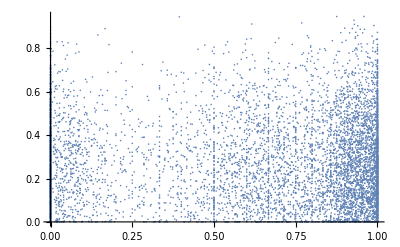

```mathematica
ListPlot[dataPFH[[All,{4,8}]]]
```

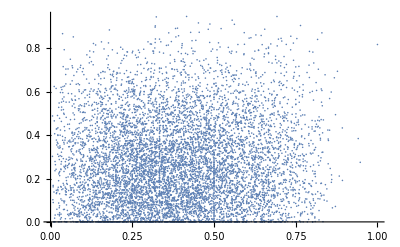

```mathematica
ListPlot[dataPFH[[All,{6,8}]]]
```

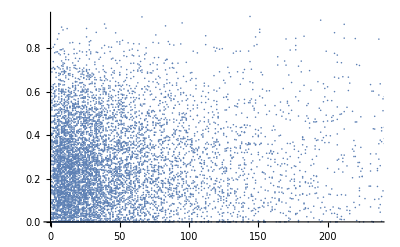

```mathematica
ListPlot[dataPFH[[All,{7,8}]]]
```

```mathematica
IndependenceTest[dataPFH[[All,4]], dataPFH[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is not rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.00100629 | 0.910747
Goodman-Kruskal γ | -0.00260084 | 0.743201
Hoeffding 𝒟 | -0.0000595988 | 0.956745
Kendall τ | -0.00252376 | 0.742019
Spearman Rank | -0.00365501 | 0.744421, | Statistic
Spearman Rank | -0.00365501}

```mathematica
IndependenceTest[dataPFH[[All,6]], dataPFH[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.0320533 | 0.00472692
Goodman-Kruskal γ | 0.0285005 | 0.000145759
Hoeffding 𝒟 | 0.000458335 | 0.000408518
Kendall τ | 0.0284456 | 0.0001456
Spearman Rank | 0.0425845 | 0.000144705, | Statistic
Spearman Rank | 0.0425845}

```mathematica
IndependenceTest[dataPFH[[All,7]], dataPFH[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.0417922 | 0.000905185
Goodman-Kruskal γ | 0.0435926 | 8.46056×10^-9
Hoeffding 𝒟 | 0.00120332 | 0.
Kendall τ | 0.0433194 | 8.42125×10^-9
Spearman Rank | 0.0645371 | 8.29738×10^-9, | Statistic
Spearman Rank | 0.0645371}

```mathematica
dataPFE = Import["~/Documents/PhD-quali/zeca-analise/prob_freq_e.csv"]
```

{{AAA,42,55,0.43299,0.56701,0.070443,97.,0.8244},{AAC,9,14,0.391304,0.608696,0.153333,23.,0.2442},{AAD,0,33,0.,1.,0.0606618,33.,0.138},{AAE,0,39,0.,1.,0.0491184,39.,0.2318},7789,{YYT,0,32,0.,1.,0.390244,32.,0.7814},{YYV,1,68,0.0144928,0.985507,0.605263,69.,0.3854},{YYW,0,9,0.,1.,0.391304,9.,0.},{YYY,0,37,0.,1.,0.435294,37.,0.3088}}
 |  |  |  |

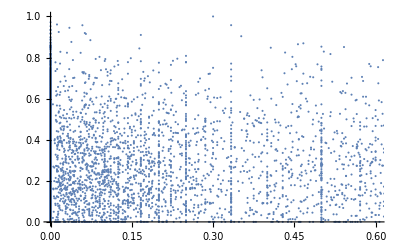

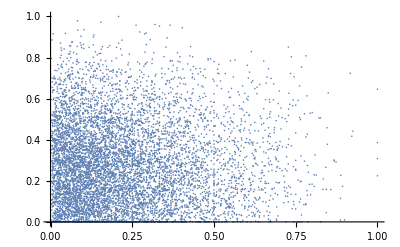

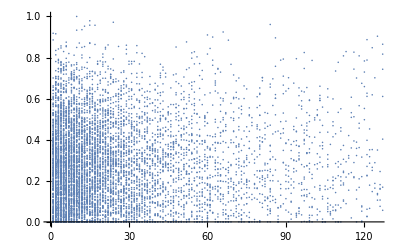

{The null hypothesis that the populations are independent is not rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | -0.00937538 | 0.
Goodman-Kruskal γ | 0.00361809 | 0.767392
Hoeffding 𝒟 | -0.0000937933 | 1.
Kendall τ | 0.00284315 | 0.73533
Spearman Rank | 0.00383212 | 0.735118, | Statistic
Spearman Rank | 0.00383212}

{The null hypothesis that the populations are independent is not rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | -0.0164239 | 0.147141
Goodman-Kruskal γ | -0.00962036 | 0.204612
Hoeffding 𝒟 | 0.0000331009 | 0.199234
Kendall τ | -0.00959989 | 0.204571
Spearman Rank | -0.014396 | 0.203716, | Statistic
Spearman Rank | -0.014396}

{The null hypothesis that the populations are independent is rejected at the 5 percent level based on the Spearman Rank test., | Statistic | P-Value
Blomqvist β | 0.0265553 | 0.11806
Goodman-Kruskal γ | 0.0208532 | 0.00703895
Hoeffding 𝒟 | 0.000244199 | 0.00814427
Kendall τ | 0.0206009 | 0.00701531
Spearman Rank | 0.0303119 | 0.0074341, | Statistic
Spearman Rank | 0.0303119}

```mathematica
ListPlot[dataPFE[[All,{4,8}]]]
ListPlot[dataPFE[[All,{6,8}]]]
ListPlot[dataPFE[[All,{7,8}]]]
IndependenceTest[dataPFE[[All,4]], dataPFE[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
IndependenceTest[dataPFE[[All,6]], dataPFE[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
IndependenceTest[dataPFE[[All,7]], dataPFE[[All,8]], {"TestConclusion", {"TestDataTable",All},"TestStatisticTable"}]
```

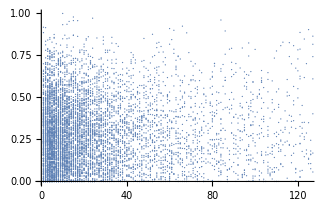

```mathematica
ListPlot[dataPFE[[All,{7,8}]]]
```